```mathematica
$HistoryLength=0;
SetDirectory["/Users/dylanbaker/Documents/GitHub/misc_classes/Spatial/notes/monte_notes/code"];
```

```mathematica
(*Workplace data*)
workplaceEmp=Flatten[Import["../input/workplaceEmp.csv"]]; (*number of jobs*)
workplaceWage=Flatten[Import["../input/workplaceWage.csv"]];(*average yearly wage of a job by workplace, dollars*)
laborIncome=(workplaceEmp workplaceWage)/10^6; (*total payment to workers in a workplace, in millions*)

(*Residence data*)
resWage=Flatten[Import["../input/residentialWage.csv"]];(*average yearly wage of a job by residence, dollars*)
resEmp=Flatten[Import["../input/residentialEmp.csv"]];(*number of residents in a residential location*)
resIncome=Flatten[Import["../input/resIncome.csv"]]; (*total residential income, millions*)

(*bilateral distances*) 
distancesOnlyTrading=Import["../input/distances_onlytrading.csv"]; (* when two counties do not trade, distance is 10^9; a row is an origin county, selling to all destination-columns counties (see below as well) *)
distancesAllPairs=Import["../input/distances_allpairs.csv"]; (*distances when all counties are allowed to trade - all bilateral distances*)

(*commuters residing in a row location and working in a column location*)
λ=Import["../input/commuting_flows.csv"];  

(*land area*)
landArea=Flatten[Import["../input/land_area.csv"]];

(*other*)
countyNames=Import["../input/county_names.csv"]; 
ncounties=Length[workplaceEmp];
mfgShares=Flatten[Import["../input/mfg_shares.csv"]];
```

```mathematica
(*saiz implied population elasticities*) 
ηzero=Table[0.,{i,1,ncounties}]; (*baseline model elasticity*) 
ηexf=Flatten[Import["../input/saiz_price_elasticities.csv"]]; (*elasticities for main exercise with positive land supply*)
```

```mathematica
beaCfs=Import["../input/bea_cfs_list.csv"];
Dimensions[beaCfs]
beaCfs[[1;;4]]
```

{3111,2}

{{3,1},{2,2},{3,3},{1,4}}

```mathematica
σ=4;
ψ=-1.2922/(1-σ);(*this ψ(1-σ) comes from the estimated gravity coefficient on CFS-level regressions*)
α=0.6;
ϵ=3.3035;
ϕ =4.4295/ϵ;
```

```mathematica
isCommuting=Table[If[λ[[i,j]]==0,0,1],{i,1,ncounties},{j,1,ncounties}];
isCommutingSp=SparseArray[isCommuting];
isNoCommuting=DiagonalMatrix[Table[1,{i,1,ncounties}]];
isNoCommutingSp=SparseArray[isNoCommuting];
```

```mathematica
population=Total[workplaceEmp];
```

```mathematica
rhsProductivities=Compile[{{prod,_Real,1},{num,_Real,2},{expenditure,_Real,1}},
Module[{bilatRes,multResistance,effDemand,leh},
bilatRes=num prod;(*proportional to bilateral cost*)
multResistance=Total[bilatRes]; (*denominator in RHS*)
effDemand=expenditure/multResistance; (*income/denominator in RHS*)
leh= bilatRes.effDemand; 
leh
](*RHS with current guess of productivity*)
];
```

```mathematica
productivities[workemp_,workwage_,resExp_,distmatrix_,detailsYN_]:=Module[{A0,λ,tol,c,dist,distmin,gap,labIncomeHat,A1,den,numerators,labIncome},
λ=0.7; (*step size *)
A0=Table[1.,{i,1,ncounties}]; (*initial condition for productivities*)

tol=10^-6; (*tolerance level*)
c=0;
dist=1;
numerators=(workemp (workwage/10^4)^(1-σ) ) (distmatrix)^(ψ(1-σ)); 
labIncome=(workemp workwage)/10^6; (*left hand side of trade flows equation*)

(*Note that the iterations solve for A^(σ-1); before returning the output, these guesses are rescaled to the 1/(σ-1).*)
While[dist>tol &&  c<10000,
c=c+1;

(*New labor Expenditure*)
labIncomeHat=rhsProductivities[A0,numerators,resExp];


 (*Relative gap in labor expenditure*)
gap=labIncome /labIncomeHat;
dist=Max[Abs[gap-1]];
distmin=Min[Abs[gap-1]];

 (*new guess of productivity*)
A1=(λ + (1-λ)gap)A0; 
den=Mean[A1];
A0=A1/den;

(*diagnostics*)
If[Mod[c,50]==1  && dist>0.01 && detailsYN==1,
Block[{},
Print["end of iteration ",c, " at " DateString[], "; min gap: ", distmin,"; max gap: ",dist,  " - ",Min[A0]," ",Max[A0]];
];
];
];
If[detailsYN==1,Block[{},
Print["end of iteration ",c, " at " DateString[], "; max gap: ",dist, " ",Min[A0]," ",Max[A0]];
]];
A0=A0^(1/(σ-1))/Mean[A0^(1/(σ-1))]; (*Recovering productivities from the A^(σ-1) values that fit the data*)
A0
];
```

```mathematica
trade=Compile[{{prod,_Real,1},{workemp,_Real,1},{workwage,_Real,1},{expenditure,_Real,1},{distmatrix,_Real,2}},
Module[{num,bilatRes,multResistance,share,trade},
num=(workemp (workwage/10^4)^(1-σ) ) (distmatrix)^(ψ(1-σ));
bilatRes=num prod^(σ-1);(*proportional to bilateral cost*)
multResistance=Total[bilatRes]; (*denominator in RHS*)
share=Transpose[Transpose[bilatRes]/multResistance ];
trade=Transpose[Transpose[share] expenditure];
{share,trade}
](*RHS with current guess of productivity*)
];
```

```mathematica
allChangesGuess=Compile[{{inWhat,_Real,1},{inλ,_Real,2},{khat,_Real,2},{dhat,_Real,2},{ahat,_Real,1},{bhat,_Real,2},{χ,_Real,1}},

allChangesGuessMod=Module[{iterVbar,iterLM,iterLR,iterQ,iterπni,iterP,iterλtilde,iterWtilde,distWages,distλ,wout,λout,diag,
temp1,temp2,temp3,temp4,temp5,temp6,denRes,numRes,den,num,den2,temp7,temp8,outcome},

(*vbar hat*)
temp1=  (λ bhat)/khat^ϵ;
denRes=temp1.inWhat^ϵ;
numRes=temp1.(inWhat^(ϵ+1) workplaceWage);
iterVbar=numRes/(resWage denRes);


(*lm hat and lr hat*)
(*note: λ are already flows, i.e. shares times Lbar in the equations*)
temp1=λ inλ;
iterLM=Total[temp1]/workplaceEmp;
iterLR=Total[Transpose[temp1]]/resEmp;


(*q hat*)

iterQ=((resIncome iterVbar iterLR+deficit)/(resIncome+deficit) )^(1/(1+χ));  

(*πni hat*)
temp1=πniOnlyTrading dhat^(1-σ);
temp2=iterLM (inWhat/ahat)^(1-σ);
den=temp2.temp1; (*note that left-product effectively gives the transpose of temp1 times temp2.*)
num=dhat^(1-σ) temp2;
iterπni=Transpose[Transpose[num]/den  ] ;(*the term inside divides each column by the correspondent element of the denominator; it then brings the matrix in the original form*)


(*P hat*)
diag=Table[iterπni[[i,i]],{i,1,ncounties}];
iterP=inWhat/ahat(iterLM/diag)^(1/(1-σ))  ;

(*w hat, next iteration*)
temp1=πniOnlyTrading iterπni;
 
temp4=iterVbar iterLR  resIncome+deficit;
iterWtilde=(temp1.temp4)/(laborIncome iterLM);
iterWtilde=iterWtilde/Mean[iterWtilde];


(*λ hat, next iteration*)
temp7=iterP^-α iterQ^(-1+α);
temp6=bhat (Outer[Times,temp7,inWhat])^ϵ/khat^ϵ;
den2=Total[Total[λ temp6]];
iterλtilde=(temp6 population)/den2 ; (*to limit accumulation of numerical errors - unconditional shares of commuting 
have a very small order of magnitude - we predict new commuting flows in # of jobs; hence, the numerator is multiplied by the population level before dividing it for the sum
of all terms at the denominator; note that the denominator contains λ, which is in fact flows of jobs, rather than shares*)

(*output: matrix with ncounties+1 rows, and ncounties columns (iterWtilde is added as a last row)*)
outcome=Join[iterλtilde,{iterWtilde}];
outcome

]
];
```

```mathematica
beaCfsCorr=Table[{},{i,1,123}];
beaCfsIndex={};
Table[Block[{},
beaCfsCorr[[ beaCfs[[n,1]] ]]=Join[beaCfsCorr[[ beaCfs[[n,1]] ]],{beaCfs[[n,2]]}];
beaCfsIndex=Join[beaCfsIndex,{Length[beaCfsCorr[[ beaCfs[[n,1]] ]]]}];
],{n,1,ncounties}];
```

```mathematica
Total[Table[Length[beaCfsCorr[[i]]],{i,1,123}]]
```

3111

```mathematica
cfsData=Import["../input/bilateral_cfs_trade.csv"];
Dimensions[cfsData]
```

{123,123}

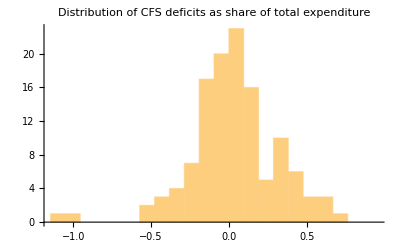

Mean: 0.033; Min: -1.145; Max: 0.952

quantile | CFS deficit
0.01 | -0.984
0.05 | -0.395
0.1 | -0.275
0.5 | 0.019
0.9 | 0.395
0.95 | 0.478
0.99 | 0.737

```mathematica
defExpenditure=(Total[cfsData]-Total[cfsData,{2}])/Total[cfsData];
Histogram[defExpenditure,{Min[defExpenditure],Quantile[defExpenditure,0.999],Quantile[defExpenditure,0.999]/10},
PlotLabel->"Distribution of CFS deficits as share of total expenditure"]
Print["Mean: ",Round[Mean[defExpenditure],0.001],"; Min: ",Round[Min[defExpenditure],0.001],"; Max: ",Round[Max[defExpenditure],0.001]];
Join[{{"quantile","CFS deficit"}},Table[{q,Quantile[Round[defExpenditure,0.001],q]},{q,{0.01,0.05,0.10,0.50,0.90,0.95,0.99}}]]//TableForm
```

```mathematica
cfsLabExp=Table[{},{i,1,123}];
Table[cfsLabExp[[k]]=Table[laborIncome[[j]],{j,beaCfsCorr[[k]]}],{k,1,123}];
cfsLabExp=Total[cfsLabExp,{2}];
Total[cfsLabExp]-Total[laborIncome]
```

1.86265×10^-9

```mathematica
rescaledCfs=cfsData/Total[cfsData,{2}]  cfsLabExp;
```

```mathematica
cfsDeficit=Total[rescaledCfs]-Total[rescaledCfs,{2}];
```

```mathematica
cfsResIncome=Table[{},{i,1,123}];
Table[cfsResIncome[[k]]=Table[resIncome[[j]],{j,beaCfsCorr[[k]]}],{k,1,123}];
increments=Table[cfsResIncome[[k]]/Total[cfsResIncome[[k]]] cfsDeficit[[k]],{k,1,123}];
resExpenditure=resIncome;
Table[resExpenditure[[i]]=resExpenditure[[i]]+ increments[[ beaCfs[[i,1]],beaCfsIndex[[i]] ]],{i,1,ncounties}];
```

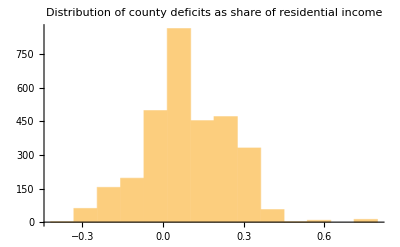

Mean: 0.092; Min: -0.418; Max: 7.1

quantile | county deficit
0.01 | -0.273
0.05 | -0.223
0.1 | -0.098
0.5 | 0.076
0.9 | 0.28
0.95 | 0.282
0.99 | 0.368

```mathematica
countyDeficit=resExpenditure/resIncome-1;

Histogram[countyDeficit,{Min[countyDeficit],Quantile[countyDeficit,0.999],Quantile[countyDeficit,0.999]/10},
PlotLabel->"Distribution of county deficits as share of residential income"]
Print["Mean: ",Round[Mean[countyDeficit],0.001],"; Min: ",Round[Min[countyDeficit],0.001],"; Max: ",Round[Max[countyDeficit],0.001]];
Join[{{"quantile","county deficit"}},Table[{q,Quantile[Round[countyDeficit,0.001],q]},{q,{0.01,0.05,0.10,0.50,0.90,0.95,0.99}}]]//TableForm
```

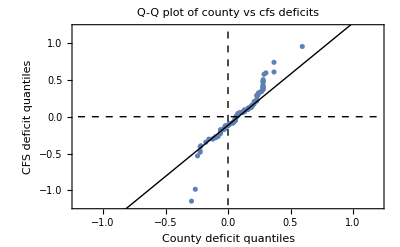

```mathematica
Show[
QuantilePlot[defExpenditure,countyDeficit,ReferenceLineStyle->Red,
FrameLabel->{"County deficit quantiles","CFS deficit quantiles"},PlotLabel->"Q-Q plot of county vs cfs deficits",PlotRange->{{-1.2,1.2},{-1.2,1.2}}],
ParametricPlot[{{0,x},{x,0}},{x,-1.2,1.2},PlotStyle->Directive[Black,Dashed,Thin]]]
```

```mathematica
deficit=resExpenditure-resIncome;
```

```mathematica
Min[resIncome+deficit]
```

0.646392

```mathematica
prodOnlyTrading=productivities[workplaceEmp,workplaceWage,resExpenditure,distancesOnlyTrading,0];
```

```mathematica
{πniOnlyTrading,tradeOnlyTrading}=trade[prodOnlyTrading,workplaceEmp,workplaceWage,resExpenditure,distancesOnlyTrading];
```

```mathematica
{Min[Total[πniOnlyTrading]],Max[Total[πniOnlyTrading]]}
{Min[Total[tradeOnlyTrading]/resExpenditure],Max[Total[tradeOnlyTrading]/resExpenditure]}
```

{1.,1.}

{1.,1.}

```mathematica
gammahatChanges[khat_,dhat_,ahat_,bhat_,landel_,outputEvery_]:=Module[{dist,c,what,λhat,inWhat,inλ,out,iterλtilde,iterWtilde,distWages,distλ,
temp1,denRes,numRes,Vbarhat,LMhat,LRhat,Qhat,temp2,den,num,πnihat,diag,Phat,pricehat,realinchat},
dist=1;
c=0;
what=Table[1,{i,1,ncounties}];
λhat=isCommuting;
gamma = 0.7;
While[c<maxiter && dist>tol,

c=c+1;
inWhat=what;
inλ=λhat;

out=allChangesGuess[inWhat,inλ,khat,dhat,ahat,bhat,landel];

iterλtilde=out[[1;;ncounties,All]] isCommutingSp;
iterWtilde=out[[ncounties+1,All]];

distWages=Max[Abs[iterWtilde/inWhat-1]];

(*using the sparse-array version of commuting allows saving time*)
distλ=Max[Abs[iterλtilde/(inλ+isCommutingSp-1) -1] isCommutingSp];
(*the denominator makes sure that the division by zero never occurs, while preserving the deviations for observed commuting pairs; then, the matrix is multiplied by commuting indicators to restore zero change where there are no commuting flows*)
what=inWhat ζ + iterWtilde (1-ζ);
λhat=inλ  ζ + iterλtilde (1-ζ);

dist=Max[{distWages,distλ}];

If[outputEvery>0 &&Mod[c,outputEvery]==1, Print["Iteration ",c,"  concluded on ",DateString[], "; distWages is ",distWages,"; distλ is ",distλ,"."]];
];
If[dist>tol,
Print["WARNING: Max iterations reached witout satisfying the required tolerance. Current sup-norm distances: distWages: ",distWages,"; distλ: ",distλ," ..."],
If[outputEvery>-1,
Print["Convergence achieved in ",c," iterations on ",DateString[],"; distWages is ",distWages,"; distλ is ",distλ," ..."]
]];

(*Computing equilibrium changes*)

(*vbar hat*)
temp1= (bhat λ)/khat^ϵ ; 
denRes=temp1.what^ϵ;
numRes=temp1.(what^(ϵ+1) workplaceWage);
Vbarhat=numRes/(resWage denRes);


(*lm hat and lr hat*)
(*note: λ are already flows, i.e. shares times Lbar in the equations*)
temp1=λ λhat;
LMhat=Total[temp1]/workplaceEmp;
LRhat=Total[Transpose[temp1]]/resEmp;


(*q hat*)

Qhat=(((resIncome Vbarhat LRhat+deficit)/(resIncome+deficit))*1/(1+ gamma))^(1/(1+landel)); 


(*πni hat*)
temp1=πniOnlyTrading dhat^(1-σ);
temp2=LMhat (what/ahat)^(1-σ);
den=temp2.temp1; (*note that left-product effectively gives the transpose of temp1 times temp2.*)
num=dhat^(1-σ) temp2;
πnihat=Transpose[Transpose[num]/den  ] ;(*the term inside divides each column by the correspondent element of the denominator; it then brings the matrix in the original form*)


(*P hat*)
diag=Table[πnihat[[i,i]],{i,1,ncounties}];
Phat=what/ahat(LMhat/diag*1/(1+ gamma))^(1/(1-σ))  ; 

(*price index hat*)
pricehat=Phat^α Qhat^(1-α);

(*real income of residents*)
realinchat=Vbarhat/pricehat; 


If[outputEvery>-1,Print["Counterfactuals completed on ",DateString[],"."]];

{what,Vbarhat,realinchat,LMhat,LRhat,Qhat,Phat,pricehat,λhat,πnihat,c,distWages,distλ}

];
```

```mathematica
(*tolerance, max number of iterations, speed of adjustment*)
tol=10^-6; maxiter=1000; ζ=0.7;
(*change in commuting costs*)
comch=(.6601334)^(1/ϵ);
khat=Table[1,{i,1,ncounties},{j,1,ncounties}];
Table[khat[[i,i]]=1,{i,1,ncounties}];

dhat=Table[1,{i,1,ncounties},{j,1,ncounties}];
ahat=Table[1,{i,1,ncounties}];
bhat=Table[1,{i,1,ncounties},{j,1,ncounties}];
```

```mathematica
khat[[1;;4,1;;4]]//MatrixForm
```

(1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1)

```mathematica
comm=gammahatChanges[khat,dhat,ahat,bhat,ηzero,25]
```

Iteration 1  concluded on Thu 30 Jan 2025 12:43:04; distWages is 9.17449×10^-7; distλ is 1.18057×10^-6.

Convergence achieved in 2 iterations on Thu 30 Jan 2025 12:43:10; distWages is 7.91126×10^-7; distλ is 4.6039×10^-7 ...

Counterfactuals completed on Thu 30 Jan 2025 12:43:13.

```mathematica
{whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,λhatOut,πnihatOut,c,distWages,distλ}=comm-1;
varnames={{"WHat"},{"VbarHat"},{"RealIncHat"},{"LMhat"},{"LRhat"},{"QHat"},{"PHat"},{"PriceHat"},{"OwnCommutingHat"},{"OwnTradeHat"},{"ownTrade"}};
```

```mathematica
ownCommHat=Diagonal[λhatOut];
ownTradeHat=Diagonal[πnihatOut];
out=Join[varnames,{whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,ownCommHat,ownTradeHat,Diagonal[πniOnlyTrading]},2];
out=Transpose[out];
out=Join[countyNames,out,2];
Export["data\\gamma_stuff.csv",out];
wel=Table[(whatOut[[i]]+1)/(khat[[i,i]] (λhatOut[[i,i]]+1)^(1/ϵ) (PhatOut[[i]]+1)^α(QhatOut[[i]]+1)^(1-α)) bhat[[i,i]]^(1/ϵ) * ((gamma/(gamma+1))^gamma - (gamma/(gamma+1))^(gamma+1)),{i,1,ncounties}];
{Min[wel],Max[wel]}
```

{0.351476,0.351476}

```mathematica
Mean[ownCommHat]
```

-6.02504×10^-9

```mathematica
λhatOut
```